# Model Comparison Figure

## Parameters

```mathematica
TextSize=20;
```

```mathematica
TicksSize=15;
```

```mathematica
GraphThickness=0.01;
```

```mathematica
LinesThickness=0.007;
```

```mathematica
ColorsDiscrete=ResourceFunction["HexToColor"]/@{"#e3f4dd","#e2f4dd","#e2f4dc","#e1f3db","#e0f3db","#e0f3da","#dff3d9","#def2d9","#def2d8","#ddf2d7","#dcf2d7","#dcf1d6","#dbf1d5","#daf1d5","#daf0d4","#d9f0d3","#d8f0d3","#d8f0d2","#d7efd1","#d6efd1","#d6efd0","#d5efcf","#d4eecf","#d3eece","#d3eecd","#d2edcd","#d1edcc","#d0edcb","#d0edcb","#cfecca","#ceecca","#cdecc9","#cdebc8","#ccebc8","#cbebc7","#caeac6","#c9eac6","#c8eac5","#c7e9c5","#c6e9c4","#c5e8c4","#c5e8c3","#c4e8c2","#c3e7c2","#c2e7c1","#c1e7c1","#c0e6c0","#bfe6c0","#bde5bf","#bce5bf","#bbe5be","#bae4be","#b9e4be","#b8e3bd","#b7e3bd","#b6e2bd","#b5e2bc","#b3e1bc","#b2e1bc","#b1e1bb","#b0e0bb","#afe0bb","#aedfbb","#acdfbb","#abdeba","#aadeba","#a9ddba","#a7ddba","#a6dcba","#a5dcba","#a3dbba","#a2dbba","#a1daba","#a0daba","#9ed9bb","#9dd9bb","#9cd8bb","#9ad8bb","#99d7bb","#98d7bc","#96d6bc","#95d6bc","#93d5bd","#92d5bd","#91d4bd","#8fd3be","#8ed3be","#8dd2be","#8bd2bf","#8ad1bf","#88d1c0","#87d0c0","#86cfc1","#84cfc1","#83cec1","#81cec2","#80cdc2","#7fccc3","#7dccc3","#7ccbc4","#7acac4","#79cac5","#77c9c5","#76c8c6","#75c8c6","#73c7c7","#72c6c7","#70c5c7","#6fc5c8","#6ec4c8","#6cc3c9","#6bc3c9","#69c2ca","#68c1ca","#67c0ca","#65bfcb","#64bfcb","#63becb","#61bdcc","#60bccc","#5fbbcc","#5dbacc","#5cb9cc","#5ab9cd","#59b8cd","#58b7cd","#57b6cd","#55b5cd","#54b4cd","#53b3cd","#51b2cd","#50b1cd","#4fb0cd","#4eafcd","#4caecd","#4badcc","#4aaccc","#49abcc","#48aacc","#46a9cb","#45a8cb","#44a6cb","#43a5ca","#42a4ca","#41a3c9","#3fa2c9","#3ea1c8","#3da0c8","#3c9ec7","#3b9dc7","#3a9cc6","#399bc6","#379ac5","#3699c5","#3597c4","#3496c4","#3395c3","#3294c2","#3193c2","#3092c1","#2f90c0","#2d8fc0","#2c8ebf","#2b8dbf","#2a8cbe","#298abd","#2889bd","#2788bc","#2687bc","#2586bb","#2485ba","#2383ba","#2282b9","#2081b9","#1f80b8","#1e7fb7","#1d7eb7","#1c7db6","#1b7bb5","#1a7ab5","#1979b4","#1978b3","#1877b3","#1776b2","#1674b1","#1573b0","#1472b0","#1371af","#1370ae","#126fad","#116dac","#106cac","#106bab","#0f6aaa","#0e69a9","#0e67a8","#0d66a7","#0d65a6","#0c64a5","#0c63a4"}
```

{RGBColor[0.8901960784313725, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8862745098039215, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8862745098039215, 0.9568627450980391, 0.8627450980392157],RGBColor[0.8823529411764706, 0.9529411764705882, 0.8588235294117647],RGBColor[0.8784313725490196, 0.9529411764705882, 0.8588235294117647],RGBColor[0.8784313725490196, 0.9529411764705882, 0.8549019607843137],RGBColor[0.8745098039215686, 0.9529411764705882, 0.8509803921568627],RGBColor[0.8705882352941177, 0.9490196078431372, 0.8509803921568627],RGBColor[0.8705882352941177, 0.9490196078431372, 0.8470588235294118],RGBColor[0.8666666666666667, 0.9490196078431372, 0.8431372549019608],RGBColor[0.8627450980392157, 0.9490196078431372, 0.8431372549019608],RGBColor[0.8627450980392157, 0.9450980392156862, 0.8392156862745098],RGBColor[0.8588235294117647, 0.9450980392156862, 0.8352941176470589],RGBColor[0.8549019607843137, 0.9450980392156862, 0.8352941176470589],RGBColor[0.8549019607843137, 0.9411764705882353, 0.8313725490196078],RGBColor[0.8509803921568627, 0.9411764705882353, 0.8274509803921568],RGBColor[0.8470588235294118, 0.9411764705882353, 0.8274509803921568],RGBColor[0.8470588235294118, 0.9411764705882353, 0.8235294117647058],RGBColor[0.8431372549019608, 0.9372549019607843, 0.8196078431372549],RGBColor[0.8392156862745098, 0.9372549019607843, 0.8196078431372549],RGBColor[0.8392156862745098, 0.9372549019607843, 0.8156862745098039],RGBColor[0.8352941176470589, 0.9372549019607843, 0.8117647058823529],RGBColor[0.8313725490196078, 0.9333333333333333, 0.8117647058823529],RGBColor[0.8274509803921568, 0.9333333333333333, 0.807843137254902],RGBColor[0.8274509803921568, 0.9333333333333333, 0.803921568627451],RGBColor[0.8235294117647058, 0.9294117647058824, 0.803921568627451],RGBColor[0.8196078431372549, 0.9294117647058824, 0.8],RGBColor[0.8156862745098039, 0.9294117647058824, 0.796078431372549],RGBColor[0.8156862745098039, 0.9294117647058824, 0.796078431372549],RGBColor[0.8117647058823529, 0.9254901960784314, 0.792156862745098],RGBColor[0.807843137254902, 0.9254901960784314, 0.792156862745098],RGBColor[0.803921568627451, 0.9254901960784314, 0.788235294117647],RGBColor[0.803921568627451, 0.9215686274509803, 0.7843137254901961],RGBColor[0.8, 0.9215686274509803, 0.7843137254901961],RGBColor[0.796078431372549, 0.9215686274509803, 0.7803921568627451],RGBColor[0.792156862745098, 0.9176470588235294, 0.7764705882352941],RGBColor[0.788235294117647, 0.9176470588235294, 0.7764705882352941],RGBColor[0.7843137254901961, 0.9176470588235294, 0.7725490196078432],RGBColor[0.7803921568627451, 0.9137254901960784, 0.7725490196078432],RGBColor[0.7764705882352941, 0.9137254901960784, 0.7686274509803921],RGBColor[0.7725490196078432, 0.9098039215686274, 0.7686274509803921],RGBColor[0.7725490196078432, 0.9098039215686274, 0.7647058823529411],RGBColor[0.7686274509803921, 0.9098039215686274, 0.7607843137254902],RGBColor[0.7647058823529411, 0.9058823529411765, 0.7607843137254902],RGBColor[0.7607843137254902, 0.9058823529411765, 0.7568627450980392],RGBColor[0.7568627450980392, 0.9058823529411765, 0.7568627450980392],RGBColor[0.7529411764705882, 0.9019607843137255, 0.7529411764705882],RGBColor[0.7490196078431373, 0.9019607843137255, 0.7529411764705882],RGBColor[0.7411764705882353, 0.8980392156862745, 0.7490196078431373],RGBColor[0.7372549019607844, 0.8980392156862745, 0.7490196078431373],RGBColor[0.7333333333333333, 0.8980392156862745, 0.7450980392156863],RGBColor[0.7294117647058823, 0.8941176470588235, 0.7450980392156863],RGBColor[0.7254901960784313, 0.8941176470588235, 0.7450980392156863],RGBColor[0.7215686274509804, 0.8901960784313725, 0.7411764705882353],RGBColor[0.7176470588235294, 0.8901960784313725, 0.7411764705882353],RGBColor[0.7137254901960784, 0.8862745098039215, 0.7411764705882353],RGBColor[0.7098039215686275, 0.8862745098039215, 0.7372549019607844],RGBColor[0.7019607843137254, 0.8823529411764706, 0.7372549019607844],RGBColor[0.6980392156862745, 0.8823529411764706, 0.7372549019607844],RGBColor[0.6941176470588235, 0.8823529411764706, 0.7333333333333333],RGBColor[0.6901960784313725, 0.8784313725490196, 0.7333333333333333],RGBColor[0.6862745098039216, 0.8784313725490196, 0.7333333333333333],RGBColor[0.6823529411764706, 0.8745098039215686, 0.7333333333333333],RGBColor[0.6745098039215687, 0.8745098039215686, 0.7333333333333333],RGBColor[0.6705882352941176, 0.8705882352941177, 0.7294117647058823],RGBColor[0.6666666666666666, 0.8705882352941177, 0.7294117647058823],RGBColor[0.6627450980392157, 0.8666666666666667, 0.7294117647058823],RGBColor[0.6549019607843137, 0.8666666666666667, 0.7294117647058823],RGBColor[0.6509803921568628, 0.8627450980392157, 0.7294117647058823],RGBColor[0.6470588235294118, 0.8627450980392157, 0.7294117647058823],RGBColor[0.6392156862745098, 0.8588235294117647, 0.7294117647058823],RGBColor[0.6352941176470588, 0.8588235294117647, 0.7294117647058823],RGBColor[0.6313725490196078, 0.8549019607843137, 0.7294117647058823],RGBColor[0.6274509803921569, 0.8549019607843137, 0.7294117647058823],RGBColor[0.6196078431372549, 0.8509803921568627, 0.7333333333333333],RGBColor[0.615686274509804, 0.8509803921568627, 0.7333333333333333],RGBColor[0.611764705882353, 0.8470588235294118, 0.7333333333333333],RGBColor[0.6039215686274509, 0.8470588235294118, 0.7333333333333333],RGBColor[0.6, 0.8431372549019608, 0.7333333333333333],RGBColor[0.596078431372549, 0.8431372549019608, 0.7372549019607844],RGBColor[0.5882352941176471, 0.8392156862745098, 0.7372549019607844],RGBColor[0.5843137254901961, 0.8392156862745098, 0.7372549019607844],RGBColor[0.5764705882352941, 0.8352941176470589, 0.7411764705882353],RGBColor[0.5725490196078431, 0.8352941176470589, 0.7411764705882353],RGBColor[0.5686274509803921, 0.8313725490196078, 0.7411764705882353],RGBColor[0.5607843137254902, 0.8274509803921568, 0.7450980392156863],RGBColor[0.5568627450980392, 0.8274509803921568, 0.7450980392156863],RGBColor[0.5529411764705883, 0.8235294117647058, 0.7450980392156863],RGBColor[0.5450980392156862, 0.8235294117647058, 0.7490196078431373],RGBColor[0.5411764705882353, 0.8196078431372549, 0.7490196078431373],RGBColor[0.5333333333333333, 0.8196078431372549, 0.7529411764705882],RGBColor[0.5294117647058824, 0.8156862745098039, 0.7529411764705882],RGBColor[0.5254901960784314, 0.8117647058823529, 0.7568627450980392],RGBColor[0.5176470588235293, 0.8117647058823529, 0.7568627450980392],RGBColor[0.5137254901960784, 0.807843137254902, 0.7568627450980392],RGBColor[0.5058823529411764, 0.807843137254902, 0.7607843137254902],RGBColor[0.5019607843137255, 0.803921568627451, 0.7607843137254902],RGBColor[0.4980392156862745, 0.8, 0.7647058823529411],RGBColor[0.49019607843137253, 0.8, 0.7647058823529411],RGBColor[0.48627450980392156, 0.796078431372549, 0.7686274509803921],RGBColor[0.4784313725490196, 0.792156862745098, 0.7686274509803921],RGBColor[0.4745098039215686, 0.792156862745098, 0.7725490196078432],RGBColor[0.4666666666666667, 0.788235294117647, 0.7725490196078432],RGBColor[0.4627450980392157, 0.7843137254901961, 0.7764705882352941],RGBColor[0.4588235294117647, 0.7843137254901961, 0.7764705882352941],RGBColor[0.45098039215686275, 0.7803921568627451, 0.7803921568627451],RGBColor[0.44705882352941173, 0.7764705882352941, 0.7803921568627451],RGBColor[0.4392156862745098, 0.7725490196078432, 0.7803921568627451],RGBColor[0.43529411764705883, 0.7725490196078432, 0.7843137254901961],RGBColor[0.43137254901960786, 0.7686274509803921, 0.7843137254901961],RGBColor[0.4235294117647059, 0.7647058823529411, 0.788235294117647],RGBColor[0.4196078431372549, 0.7647058823529411, 0.788235294117647],RGBColor[0.4117647058823529, 0.7607843137254902, 0.792156862745098],RGBColor[0.40784313725490196, 0.7568627450980392, 0.792156862745098],RGBColor[0.403921568627451, 0.7529411764705882, 0.792156862745098],RGBColor[0.396078431372549, 0.7490196078431373, 0.796078431372549],RGBColor[0.39215686274509803, 0.7490196078431373, 0.796078431372549],RGBColor[0.38823529411764707, 0.7450980392156863, 0.796078431372549],RGBColor[0.3803921568627451, 0.7411764705882353, 0.8],RGBColor[0.3764705882352941, 0.7372549019607844, 0.8],RGBColor[0.37254901960784315, 0.7333333333333333, 0.8],RGBColor[0.36470588235294116, 0.7294117647058823, 0.8],RGBColor[0.3607843137254902, 0.7254901960784313, 0.8],RGBColor[0.3529411764705882, 0.7254901960784313, 0.803921568627451],RGBColor[0.34901960784313724, 0.7215686274509804, 0.803921568627451],RGBColor[0.34509803921568627, 0.7176470588235294, 0.803921568627451],RGBColor[0.3411764705882353, 0.7137254901960784, 0.803921568627451],RGBColor[0.3333333333333333, 0.7098039215686275, 0.803921568627451],RGBColor[0.32941176470588235, 0.7058823529411764, 0.803921568627451],RGBColor[0.3254901960784314, 0.7019607843137254, 0.803921568627451],RGBColor[0.3176470588235294, 0.6980392156862745, 0.803921568627451],RGBColor[0.3137254901960784, 0.6941176470588235, 0.803921568627451],RGBColor[0.30980392156862746, 0.6901960784313725, 0.803921568627451],RGBColor[0.3058823529411765, 0.6862745098039216, 0.803921568627451],RGBColor[0.2980392156862745, 0.6823529411764706, 0.803921568627451],RGBColor[0.29411764705882354, 0.6784313725490196, 0.8],RGBColor[0.2901960784313725, 0.6745098039215687, 0.8],RGBColor[0.28627450980392155, 0.6705882352941176, 0.8],RGBColor[0.2823529411764706, 0.6666666666666666, 0.8],RGBColor[0.27450980392156865, 0.6627450980392157, 0.796078431372549],RGBColor[0.27058823529411763, 0.6588235294117647, 0.796078431372549],RGBColor[0.26666666666666666, 0.6509803921568628, 0.796078431372549],RGBColor[0.2627450980392157, 0.6470588235294118, 0.792156862745098],RGBColor[0.2588235294117647, 0.6431372549019607, 0.792156862745098],RGBColor[0.2549019607843137, 0.6392156862745098, 0.788235294117647],RGBColor[0.24705882352941178, 0.6352941176470588, 0.788235294117647],RGBColor[0.24313725490196078, 0.6313725490196078, 0.7843137254901961],RGBColor[0.2392156862745098, 0.6274509803921569, 0.7843137254901961],RGBColor[0.23529411764705882, 0.6196078431372549, 0.7803921568627451],RGBColor[0.23137254901960785, 0.615686274509804, 0.7803921568627451],RGBColor[0.22745098039215686, 0.611764705882353, 0.7764705882352941],RGBColor[0.22352941176470587, 0.6078431372549019, 0.7764705882352941],RGBColor[0.21568627450980393, 0.6039215686274509, 0.7725490196078432],RGBColor[0.21176470588235294, 0.6, 0.7725490196078432],RGBColor[0.20784313725490194, 0.592156862745098, 0.7686274509803921],RGBColor[0.20392156862745098, 0.5882352941176471, 0.7686274509803921],RGBColor[0.2, 0.5843137254901961, 0.7647058823529411],RGBColor[0.19607843137254902, 0.580392156862745, 0.7607843137254902],RGBColor[0.19215686274509802, 0.5764705882352941, 0.7607843137254902],RGBColor[0.18823529411764706, 0.5725490196078431, 0.7568627450980392],RGBColor[0.1843137254901961, 0.5647058823529412, 0.7529411764705882],RGBColor[0.1764705882352941, 0.5607843137254902, 0.7529411764705882],RGBColor[0.17254901960784313, 0.5568627450980392, 0.7490196078431373],RGBColor[0.16862745098039217, 0.5529411764705883, 0.7490196078431373],RGBColor[0.16470588235294117, 0.5490196078431373, 0.7450980392156863],RGBColor[0.16078431372549018, 0.5411764705882353, 0.7411764705882353],RGBColor[0.1568627450980392, 0.5372549019607843, 0.7411764705882353],RGBColor[0.15294117647058825, 0.5333333333333333, 0.7372549019607844],RGBColor[0.14901960784313725, 0.5294117647058824, 0.7372549019607844],RGBColor[0.14509803921568626, 0.5254901960784314, 0.7333333333333333],RGBColor[0.1411764705882353, 0.5215686274509804, 0.7294117647058823],RGBColor[0.13725490196078433, 0.5137254901960784, 0.7294117647058823],RGBColor[0.13333333333333333, 0.5098039215686274, 0.7254901960784313],RGBColor[0.12549019607843137, 0.5058823529411764, 0.7254901960784313],RGBColor[0.12156862745098039, 0.5019607843137255, 0.7215686274509804],RGBColor[0.11764705882352941, 0.4980392156862745, 0.7176470588235294],RGBColor[0.11372549019607843, 0.49411764705882355, 0.7176470588235294],RGBColor[0.10980392156862745, 0.49019607843137253, 0.7137254901960784],RGBColor[0.10588235294117647, 0.4823529411764706, 0.7098039215686275],RGBColor[0.10196078431372549, 0.4784313725490196, 0.7098039215686275],RGBColor[0.09803921568627451, 0.4745098039215686, 0.7058823529411764],RGBColor[0.09803921568627451, 0.47058823529411764, 0.7019607843137254],RGBColor[0.09411764705882353, 0.4666666666666667, 0.7019607843137254],RGBColor[0.09019607843137255, 0.4627450980392157, 0.6980392156862745],RGBColor[0.08627450980392157, 0.4549019607843137, 0.6941176470588235],RGBColor[0.08235294117647059, 0.45098039215686275, 0.6901960784313725],RGBColor[0.0784313725490196, 0.44705882352941173, 0.6901960784313725],RGBColor[0.07450980392156863, 0.44313725490196076, 0.6862745098039216],RGBColor[0.07450980392156863, 0.4392156862745098, 0.6823529411764706],RGBColor[0.07058823529411765, 0.43529411764705883, 0.6784313725490196],RGBColor[0.06666666666666667, 0.42745098039215684, 0.6745098039215687],RGBColor[0.06274509803921569, 0.4235294117647059, 0.6745098039215687],RGBColor[0.06274509803921569, 0.4196078431372549, 0.6705882352941176],RGBColor[0.058823529411764705, 0.4156862745098039, 0.6666666666666666],RGBColor[0.054901960784313725, 0.4117647058823529, 0.6627450980392157],RGBColor[0.054901960784313725, 0.403921568627451, 0.6588235294117647],RGBColor[0.050980392156862744, 0.4, 0.6549019607843137],RGBColor[0.050980392156862744, 0.396078431372549, 0.6509803921568628],RGBColor[0.047058823529411764, 0.39215686274509803, 0.6470588235294118],RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]}

```mathematica
ColorGradient=Blend[ColorsDiscrete,#]&
```

Blend[ColorsDiscrete,#1]&

```mathematica
color1=RGBColor[0.047058823529411764,0.38823529411764707,0.6431372549019607]
```

RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]

```mathematica
color2=RGBColor[0.5769319492502883,0.8355247981545559,0.7409457900807382]
```

RGBColor[0.5769319492502883, 0.8355247981545559, 0.7409457900807382]

```mathematica
UpperError[Points_,Errors_]:=MapThread[Function[{pt,err},{pt[[1]],pt[[2]]+err}],{Points,Errors}]
```

```mathematica
LowerError[Points_,Errors_]:= MapThread[Function[{pt, err},{pt[[1]], Max[pt[[2]] - err, $MachineEpsilon]}  ],{Points, Errors}]
```

## Boston

## Theory

```mathematica
f[i_,k_,β_]:=(k*β)/(2-β)Gamma[i]/Pochhammer[2+1/(1-β),-1+i]
```

## Data

### Violent

#### Real Data

```mathematica
SetDirectory["..."]
```

```mathematica
AlphaViolentBoston=Flatten[Import["Alpha_Violent_Crime_2015-2024_Boston.mat"]]
```

{0.687535,0.766596,0.886838,0.80311,0.879228,0.925977,0.87864,0.922665,0.891818}

```mathematica
AlphaViolent2023Boston=AlphaViolentBoston[[-2]]
```

0.922665

```mathematica
BostonViolentCrime2023=Flatten[Import["Annual_Crime_Violent_Crime_2023_Boston.mat"]];
```

```mathematica
BostonViolentCrimeBlock2023=Length[BostonViolentCrime2023]
```

5918

```mathematica
BostonTotalViolent2023=Total[BostonViolentCrime2023]
```

2252.

```mathematica
BostonViolentCrimeNoZero2023=Select[BostonViolentCrime2023,#>0&];
```

```mathematica
BostonViolentCrimeCounts2023=SortBy[Tally[BostonViolentCrimeNoZero2023],First]
```

{{1.,674},{2.,205},{3.,71},{4.,44},{5.,21},{6.,14},{7.,7},{8.,6},{9.,7},{10.,3},{11.,3},{12.,3},{13.,2},{14.,2},{15.,1},{16.,1},{17.,2},{18.,1},{20.,1},{25.,2},{28.,1},{29.,1},{33.,1},{34.,1}}

```mathematica
BostonViolentCrimeNoZeroBlock2023=Total[BostonViolentCrimeCounts2023[[All,2]]]
```

1074

```mathematica
βViolent=Solve[BostonTotalViolent2023*p==BostonViolentCrimeNoZeroBlock2023,p]
```

{{p→0.476909}}

```mathematica
βViolent=p/.βViolent[[1]]
```

0.476909

#### Simulation

```mathematica
SetDirectory["..."]
```

```mathematica
BostonViolentCrimeSimulation2023=Partition[Riffle[Flatten[Import["Violent_Crime_2023_Boston_Simulation_Crime_Number.mat"]],Flatten[Import["Violent_Crime_2023_Boston_Simulation_Mean_Block_Number.mat"]]],2];
```

```mathematica
BostonViolentCrimeSimulation2023Errors=Flatten[Import["Violent_Crime_2023_Boston_Simulation_Errors.mat"]];
```

```mathematica
BostonViolentCrimeSimulation2023Plus=UpperError[BostonViolentCrimeSimulation2023,BostonViolentCrimeSimulation2023Errors];
```

```mathematica
BostonViolentCrimeSimulation2023Minus=LowerError[BostonViolentCrimeSimulation2023,BostonViolentCrimeSimulation2023Errors];
```

```mathematica
simAssocViolentBoston=Association[Rule@@@BostonViolentCrimeSimulation2023];
```

```mathematica
BostonRealVSPredictionViolent2023=BostonViolentCrimeCounts2023/. {x_,y1_}:>{y1,Lookup[simAssocViolentBoston,x,Missing["NotFound"]]}
```

{{674,685.87},{205,186.37},{71,80.09},{44,40.51},{21,24.29},{14,15.04},{7,9.58},{6,7.08},{7,4.96},{3,3.79},{3,3.27},{3,2.38},{2,1.81},{2,1.59},{1,1.14},{1,0.87},{2,0.85},{1,0.7},{1,0.59},{2,0.27},{1,0.27},{1,0.16},{1,0.09},{1,0.12}}

### Property

#### Real Data

```mathematica
SetDirectory["..."]
```

```mathematica
AlphaPropertyBoston=Flatten[Import["Alpha_Property_Crime_2015-2024_Boston.mat"]]
```

{0.754092,0.805252,0.829356,0.824042,0.986419,0.903684,0.880551,0.846766,0.946379}

```mathematica
AlphaProperty2023Boston=AlphaPropertyBoston[[-2]]
```

0.846766

```mathematica
BostonPropertyCrime2023=Flatten[Import["Annual_Crime_Property_Crime_2023_Boston.mat"]];
```

```mathematica
BostonPropertyCrimeBlock2023=Length[BostonPropertyCrime2023]
```

5918

```mathematica
BostonTotalProperty2023=Total[BostonPropertyCrime2023]
```

11255.

```mathematica
BostonPropertyCrimeNoZero2023=Select[BostonPropertyCrime2023,#>0&];
```

```mathematica
BostonPropertyCrimeCounts2023=SortBy[Tally[BostonPropertyCrimeNoZero2023],First]
```

{{1.,1041},{2.,441},{3.,231},{4.,133},{5.,71},{6.,49},{7.,28},{8.,30},{9.,10},{10.,14},{11.,9},{12.,10},{13.,6},{14.,6},{15.,8},{16.,5},{17.,3},{18.,2},{19.,3},{20.,2},{21.,2},{22.,1},{24.,1},{25.,4},{27.,2},{30.,3},{31.,1},{32.,1},{34.,1},{36.,2},{38.,2},{41.,1},{42.,1},{43.,1},{44.,1},{46.,2},{47.,2},{60.,1},{68.,2},{80.,1},{96.,1},{105.,1},{109.,1},{133.,1},{143.,1},{146.,1},{176.,1},{188.,1},{189.,1},{246.,1},{268.,2},{276.,1},{306.,1},{424.,1},{436.,1},{551.,1},{758.,1}}

```mathematica
BostonPropertyCrimeNoZeroBlock2023=Total[BostonPropertyCrimeCounts2023[[All,2]]]
```

2152

```mathematica
βProperty=Solve[BostonTotalProperty2023*p==BostonPropertyCrimeNoZeroBlock2023,p]
```

{{p→0.191204}}

```mathematica
βProperty=p/.βProperty[[1]]
```

0.191204

#### Simulation

```mathematica
SetDirectory["..."]
```

```mathematica
BostonPropertyCrimeSimulation2023=Partition[Riffle[Flatten[Import["Property_Crime_2023_Boston_Simulation_Crime_Number.mat"]],Flatten[Import["Property_Crime_2023_Boston_Simulation_Mean_Block_Number.mat"]]],2]
```

```mathematica
BostonPropertyCrimeSimulation2023Errors=Flatten[Import["Property_Crime_2023_Boston_Simulation_Errors.mat"]];
```

```mathematica
BostonPropertyCrimeSimulation2023Plus=UpperError[BostonPropertyCrimeSimulation2023,BostonPropertyCrimeSimulation2023Errors];
```

```mathematica
BostonPropertyCrimeSimulation2023Minus=LowerError[BostonPropertyCrimeSimulation2023,BostonPropertyCrimeSimulation2023Errors];
```

```mathematica
simAssocPropertyBoston=Association[Rule@@@BostonPropertyCrimeSimulation2023]
```

```mathematica
BostonRealVSPredictionProperty2023=BostonPropertyCrimeCounts2023/. {x_,y1_}:>{y1,Lookup[simAssocPropertyBoston,x,Missing["NotFound"]]}
```

{{1041,980.76},{441,372.97},{231,197.77},{133,122.91},{71,84.4},{49,59.72},{28,45.72},{30,36.04},{10,28.54},{14,24.21},{9,20.07},{10,16.66},{6,14.13},{6,12.47},{8,10.5},{5,9.08},{3,8.59},{2,7.35},{3,6.26},{2,5.54},{2,5.44},{1,5.03},{1,4.05},{4,3.85},{2,3.34},{3,2.72},{1,2.15},{1,2.24},{1,1.87},{2,1.7},{2,1.44},{1,1.28},{1,1.11},{1,1.07},{1,1.23},{2,1.},{2,0.93},{1,0.64},{2,0.37},{1,0.3},{1,0.17},{1,0.09},{1,0.1},{1,0.06},{1,0.1},{1,0.05},{1,0.03},{1,0.04},{1,0.04},{1,0.02},{2,0.},{1,0.01},{1,0.02},{1,0.01},{1,0.01},{1,0.},{1,0.}}

## Plotting

## Violent Crime

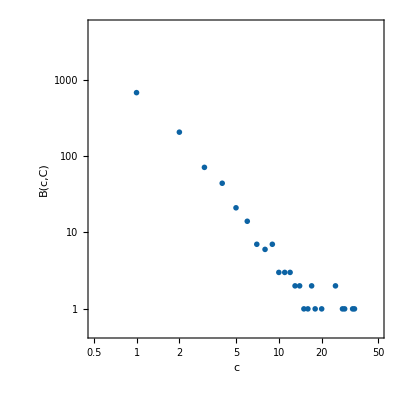

```mathematica
BostonViolentDataPlot=ListLogLogPlot[BostonViolentCrimeCounts2023,PlotRange->{{5*10^-1,50},{0.5,5*10^3}},Frame->True,AspectRatio->1,PlotMarkers->{Graphics[{Style[Disk[],color1]}],2GraphThickness},GridLines->{{5×10^0,5×10^1,5×10^2,5×10^3},{5×10^0,5×10^1,5×10^2,5×10^3,5×10^4,5×10^5}},FrameLabel->{Style["c",Italic,TextSize,FontFamily->"Arial"],Style["B(c,C)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"},{5×10^4,"5×10^4"},{5×10^5,"5×10^5"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize]]
```

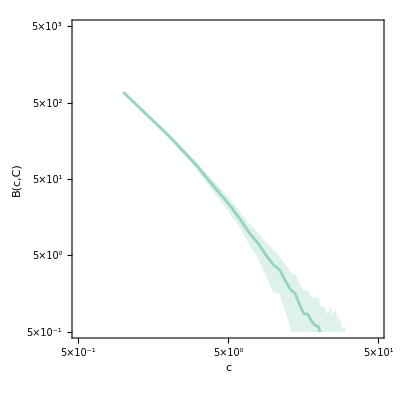

```mathematica
BostonViolentSimulationPlot=ListLinePlot[{BostonViolentCrimeSimulation2023,BostonViolentCrimeSimulation2023Minus,BostonViolentCrimeSimulation2023Plus},PlotRange->{{5*10^-1,50},{0.5,5*10^3}},Frame->True,AspectRatio->1,PlotStyle->{{color2,GraphThickness},None,None},FillingStyle->Directive[color2,Opacity[0.3]],GridLines->{{5×10^0,5×10^1,5×10^2,5×10^3},{5×10^0,5×10^1,5×10^2,5×10^3,5×10^4,5×10^5}},FrameLabel->{Style["c",Italic,TextSize,FontFamily->"Arial"],Style["B(c,C)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"},{5×10^4,"5×10^4"},{5×10^5,"5×10^5"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],Filling->{2->{3}},ScalingFunctions->{"Log","Log"}]
```

General::munfl: 1/(1.46576×10^308) is too small to represent as a normalized machine number; precision may be lost.

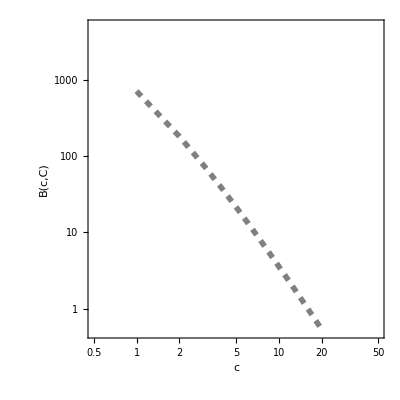

```mathematica
BostonViolentTheorySimplePlot=ListLogLogPlot[Table[{i,f[i,BostonTotalViolent2023,βViolent]},{i,1,Max[BostonViolentCrimeCounts2023[[All,2]]]}],Joined->True,PlotRange->{{5*10^-1,50},{0.5,5*10^3}},Frame->True,AspectRatio->1,PlotStyle->{Gray,Dashed,Thickness[GraphThickness]},GridLines->{{5×10^0,5×10^1,5×10^2,5×10^3},{5×10^0,5×10^1,5×10^2,5×10^3,5×10^4,5×10^5}},FrameLabel->{Style["c",Italic,TextSize,FontFamily->"Arial"],Style["B(c,C)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"},{5×10^4,"5×10^4"},{5×10^5,"5×10^5"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize]]
```

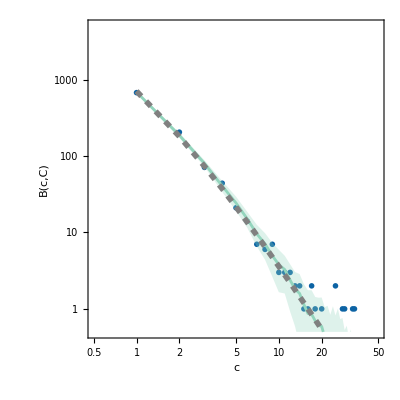

```mathematica
Show[BostonViolentDataPlot,BostonViolentSimulationPlot,BostonViolentTheorySimplePlot]
```

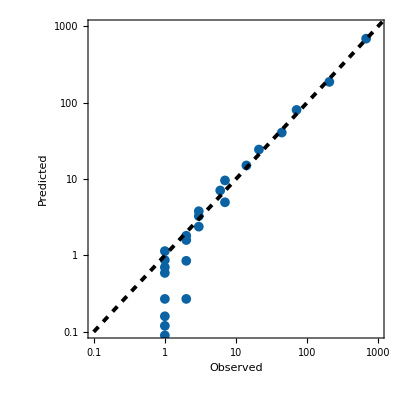

```mathematica
Show[ListLogLogPlot[BostonRealVSPredictionViolent2023,PlotRange->{{10^-1,10^3},{10^-1,10^3}},Frame->True,AspectRatio->1,PlotMarkers->Graphics[{Directive[color1],Disk[]},ImageSize->10],GridLines->Automatic,FrameLabel->{Style["Observed",TextSize,FontFamily->"Arial"],Style["Predicted",TextSize,FontFamily->"Arial"]},FrameTicks->{{{{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}},None},{{{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize]],LogLogPlot[x,{x,0.1,10^5},PlotStyle->{Thickness[LinesThickness],Dashed,Black}]]
```

## Property Crime

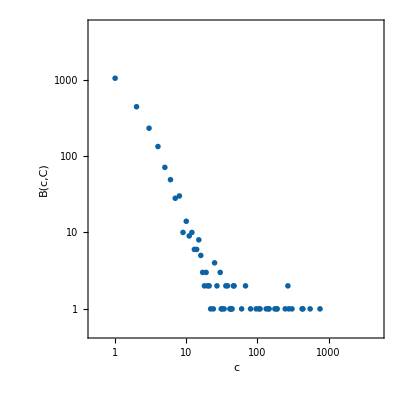

```mathematica
BostonPropertyDataPlot=ListLogLogPlot[BostonPropertyCrimeCounts2023,PlotRange->{{0.5,5*10^3},{0.5,5×10^3}},Frame->True,AspectRatio->1,PlotMarkers->{Graphics[{Style[Disk[],color1]}],2GraphThickness},GridLines->{{5×10^0,5×10^1,5×10^2,5×10^3},{5×10^0,5×10^1,5×10^2,5×10^3,5×10^4,5×10^5}},FrameLabel->{Style["c",Italic,TextSize,FontFamily->"Arial"],Style["B(c,C)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"},{5×10^4,"5×10^4"},{5×10^5,"5×10^5"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize]]
```

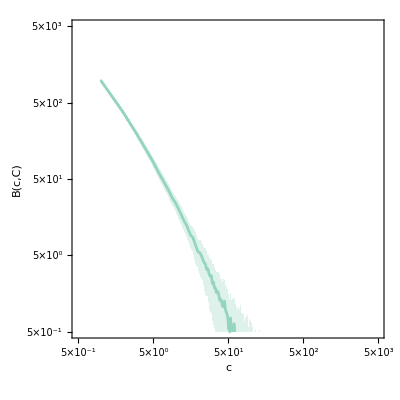

```mathematica
BostonPropertySimulationPlot=ListLinePlot[{BostonPropertyCrimeSimulation2023,BostonPropertyCrimeSimulation2023Minus,BostonPropertyCrimeSimulation2023Plus},PlotRange->{{0.5,5*10^3},{0.5,5×10^3}},Frame->True,AspectRatio->1,PlotStyle->{{color2,GraphThickness},None,None},FillingStyle->Directive[color2,Opacity[0.3]],GridLines->{{5×10^0,5×10^1,5×10^2,5×10^3},{5×10^0,5×10^1,5×10^2,5×10^3,5×10^4,5×10^5}},FrameLabel->{Style["c",Italic,TextSize,FontFamily->"Arial"],Style["B(c,C)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"},{5×10^4,"5×10^4"},{5×10^5,"5×10^5"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],Filling->{2->{3}},ScalingFunctions->{"Log","Log"}]
```

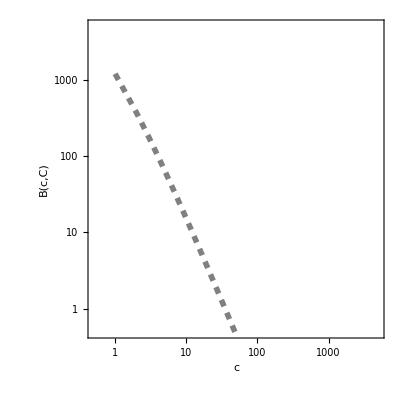

```mathematica
BostonPropertyTheorySimplePlot=ListLogLogPlot[Table[{i,f[i,BostonTotalProperty2023,βProperty]},{i,1,Max[BostonPropertyCrimeCounts2023[[All,2]]]}],Joined->True,PlotRange->{{0.5,5*10^3},{0.5,5×10^3}},Frame->True,AspectRatio->1,PlotStyle->{Gray,Dashed,Thickness[GraphThickness]},GridLines->{{5×10^0,5×10^1,5×10^2,5×10^3},{5×10^0,5×10^1,5×10^2,5×10^3,5×10^4,5×10^5}},FrameLabel->{Style["c",Italic,TextSize,FontFamily->"Arial"],Style["B(c,C)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"},{5×10^4,"5×10^4"},{5×10^5,"5×10^5"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize]]
```

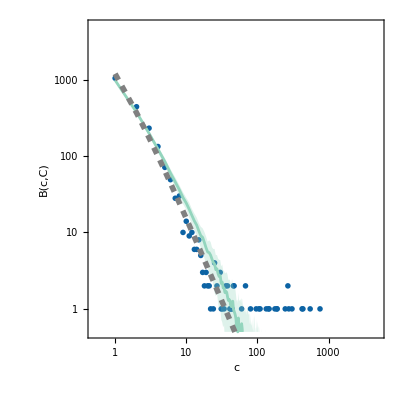

```mathematica
Show[BostonPropertyDataPlot,BostonPropertySimulationPlot,BostonPropertyTheorySimplePlot]
```

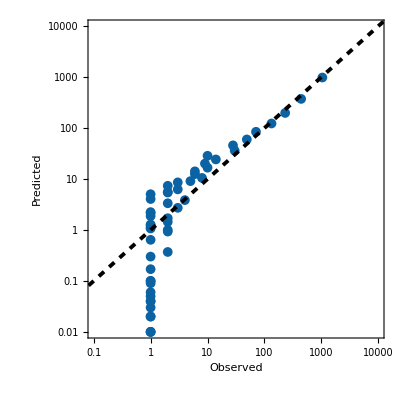

```mathematica
Show[ListLogLogPlot[BostonRealVSPredictionProperty2023,PlotRange->{{10^-1,10^4},{10^-2,10^4}},Frame->True,AspectRatio->1,PlotMarkers->Graphics[{Directive[color1],Disk[]},ImageSize->10],GridLines->Automatic,FrameLabel->{Style["Observed",TextSize,FontFamily->"Arial"],Style["Predicted",TextSize,FontFamily->"Arial"]},FrameTicks->{{{{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}},None},{{{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}},None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize]],LogLogPlot[x,{x,0.01,10^5},PlotStyle->{Thickness[LinesThickness],Dashed,Black}]]
```